Calculating how long between outcoupling pulses one has to wait before the pulses will be overlapped in time when they hit the detector.

The first approach is to consider that at each outcoupling there are two particles one travelling down with vmax and the other travelling up at vmax. Lets consider the +vmax particle in one pulse and the -vmax in the next pulse. These will always cross each other given enough time, the case we care about is if they cross at or before the detector. So we will constrain that they cross at the detector (xdet).

-(g t^2)/2+t vmax

-1/2 g (-d+t)^2-(-d+t) vmax

{vmax→10,g→10,d→1.9}

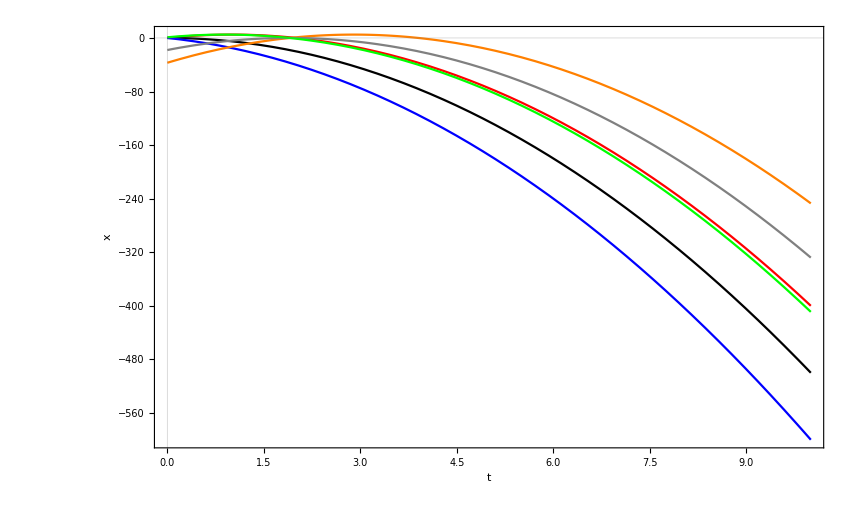

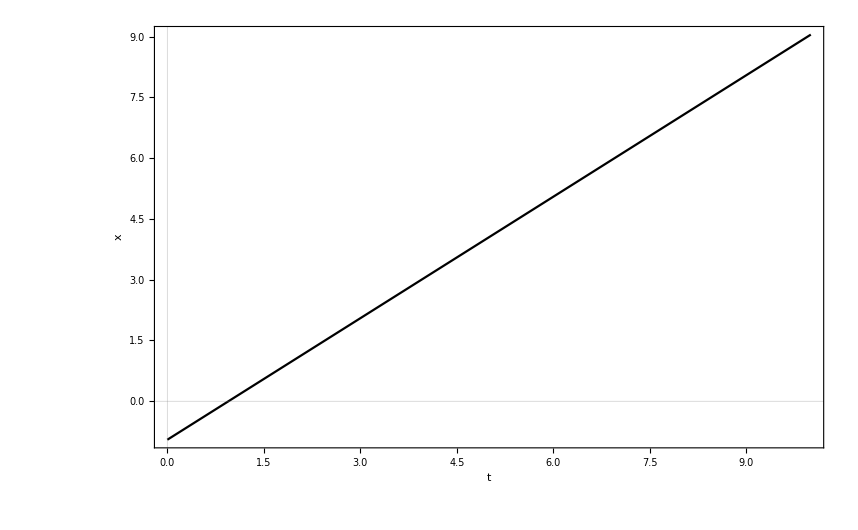

```mathematica
eq1= vmax *t -1/2 g (t^2) 
eq2= -vmax *(t-d) -1/2 g((t-d)^2)
defaults={vmax->10,g->10,d->1.9}
Plot[
{
eq1/.defaults,
eq1/.{vmax->0}/.defaults,
eq1/.{vmax->-vmax}/.defaults,
eq2/.{vmax->-vmax}/.defaults,
eq2/.{vmax->0}/.defaults,
eq2/.defaults
},
{t,0,10},
PlotTheme->"Scientific",FrameLabel->{"t","x"},
PlotStyle->{{Red},{Black},{Blue},{Orange},{Gray},{Green}}]

Plot[
{(eq1/.defaults)-(eq2/.defaults)},
{t,0,10},PlotTheme->"Scientific",FrameLabel->{"t","x"},PlotStyle->{{Black}}]
```

```mathematica
{eq1,eq2}/.{vmax->10^-2,g->10}
```

{t/100-5 t^2,(d-t)/100-5 (-d+t)^2}

```mathematica
sln=Solve[{eq1==-xdet,eq2==-xdet},{t,d} ]
```

{{t→(vmax-√(vmax^2+2 g xdet))/g,d→(2 vmax)/g},{t→(vmax-√(vmax^2+2 g xdet))/g,d→2 (vmax/g-(√(vmax^2+2 g xdet))/g)},{t→(vmax+√(vmax^2+2 g xdet))/g,d→(2 vmax)/g},{t→(vmax+√(vmax^2+2 g xdet))/g,d→2 (vmax/g+(√(vmax^2+2 g xdet))/g)}}

```mathematica
N[sln/.{vmax->10,g->1,xdet->10}] {vmax->10,g->10,d->1.9}
```

{{t→-0.954451,d→20.},{t→-0.954451,d→-1.9089},{t→20.9545,d→20.},{t→20.9545,d→41.9089}}

The next apprach is to consider that in each outcoupling pulse  there is a (negligible population) trajectory that outcouples directly falls back directly down  and bounces off the bec, then on the second time it falls just missing the bec. THis is an